# Model Error for Exponential

-Graphics-

Bias from assumption is given as ξ.

```mathematica
ξ=(Exp[r(1+δ)t]+Exp[r(1-δ)t])/(2Exp[r t])//FullSimplify
```

Cosh[r t δ]

Take rate of change of this.

```mathematica
D[ξ,δ]//FullSimplify
```

r t Sinh[r t δ]

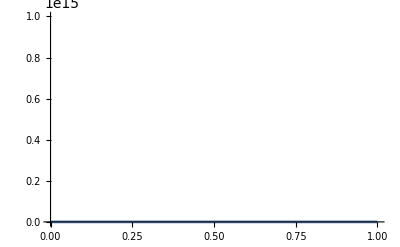

```mathematica
Plot[{ξ/.r->10,ξ/.r->50}/.t->2,{δ,0,1}]
```